```mathematica
Series[1/(1+x),{x,0,2}]
```

1-x+x^2+O[x]^3

```mathematica
G[ω_]:=1/(1/2(2-I ω+ ((2-ω I )^2-4)^{1/2}))
```

```mathematica
G[0]
```

{1}

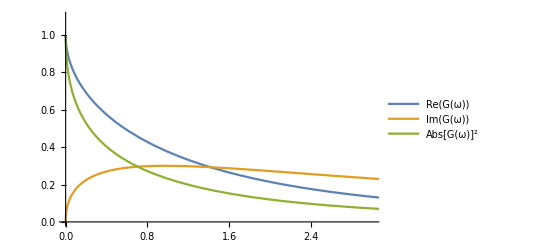

```mathematica
Plot[{Re[G[ω]],Im[G[ω]],Abs[G[ω]]^2},{ω,0,6},PlotRange->{{0,3},{0,1.1}},PlotLegends->"Expressions"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["G(w).jpeg",Plot[{Re[G[ω]],Im[G[ω]],Abs[G[ω]]^2},{ω,0,6},PlotRange->{{0,3},{0,1.1}},PlotLegends->"Expressions"]];
```

/home/k1762355/Documents/research_methods/mathematica

```mathematica
Im[G[ω]]
```

{2 Im[1/(2-ⅈ √(-4+(2-ⅈ ω)^2) ω)]}

```mathematica
Series[G[ω]/ω,{ω,0,2}]
```

{1/ω+(-1)^(3/4)/(√ω)-ⅈ/2+1/8 (-1)^(1/4) √ω+1/128 (-1)^(3/4) ω^(3/2)+O[ω]^(5/2)}

```mathematica
Im[(-1)^(3/4)]
```

1/(√2)